# Learning XOR

```mathematica
Get["neural-logic.m",Path->SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/prototype"]]
```

## Get data

```mathematica
numBooleanVariables=20; (* 2^numBooleanVariables possible inputs *)
bf=BooleanConvert[Xor[#1,#2,#3,#4,#5,#6,#7,#8,#9,#10,#11,#12,#13,#14,#15,#16,#17,#18,#19,#20]&,"BooleanFunction"];
maxExamples=Min[10000,2^numBooleanVariables];
numClasses=2;
examples=Map[With[{x=RandomChoice[{0,1},numBooleanVariables]},Soften/@x->bf@@x]&,Range[maxExamples]];
```

```mathematica
Take[examples,3]
```

{{1.,0.,1.,1.,1.,0.,0.,0.,1.,1.,0.,0.,0.,1.,1.,1.,0.,0.,1.,0.}→False,{0.,1.,1.,1.,1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.}→False,{0.,0.,0.,1.,1.,0.,1.,1.,0.,1.,0.,1.,0.,0.,1.,0.,0.,1.,0.,0.}→False}

```mathematica
{trainData,testData}=[examples,"TestSetSize"->Scaled[0.2],"Shuffle"->True];
```

## Create feature encoders

```mathematica
inputSize=Length[First[First[trainData]]];
```

```mathematica
targetEncoder=NetEncoder[{"Class",{True,False},"IndicatorVector"}];
```

## Create net

```mathematica
{softNet,hardNet}=With[{classificationLayerSize=32*numClasses},
HardNeuralChain[{
HardNeuralNOT[inputSize,classificationLayerSize],
HardNeuralMajority[classificationLayerSize,inputSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
{softNet,hardNet}=With[{classificationLayerSize=64*numClasses},
HardNeuralChain[{
HardNeuralNAND[inputSize,classificationLayerSize],
HardNeuralNAND[classificationLayerSize,classificationLayerSize],
HardNeuralReshapeLayer[classificationLayerSize,numClasses]
}]];
```

```mathematica
trainableSoftNet=NetGraph[<|"NeuralLogicNet"->softNet,"Loss"->HardClassificationLoss[]|>,{"NeuralLogicNet"->"Loss"},"Target"->targetEncoder];
```

```mathematica
NetFlatten[trainableSoftNet]
```

NetGraph[<>]

## Train net

```mathematica
result=NetTrain[trainableSoftNet,trainData,All,
ValidationSet->testData,
LossFunction->"Loss",
Method->{"ADAM"},
TargetDevice->"GPU",
MaxTrainingRounds->20000];
```

## Evaluate soft net

```mathematica
{trainedSoftNet,trainedHardNet}=NetGraph[
<|"TrainedNet"->NetDelete[NetFlatten[#],"Loss/Error"]|>,{},
"Output"->NetDecoder[targetEncoder]]&/@{result["TrainedNet"],HardenNet[result["TrainedNet"]
]};
```

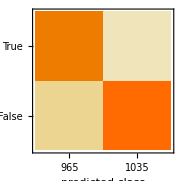
{Classifier Measurements
Classifier method | Net
Number of test examples | 2000
Accuracy | (99.750.11) %
Accuracy baseline | (51.91.1) %
Geometric mean of probabilities | 0.974 ± 0.0018
Mean cross entropy | 0.0261 ± 0.0018
Single evaluation time | 3.14 ms/example
Batch evaluation speed | 33.8 examples/ms
-Graphics- | ,Classifier Measurements
Classifier method | Net
Number of test examples | 2000
Accuracy | (99.750.11) %
Accuracy baseline | (51.91.1) %
Geometric mean of probabilities | 0.974 ± 0.0018
Mean cross entropy | 0.0261 ± 0.0018
Single evaluation time | 3.18 ms/example
Batch evaluation speed | 31.6 examples/ms
-Graphics- | }

```mathematica
ClassifierMeasurements[#,testData]&/@{trainedSoftNet,trainedHardNet}
```

## Evaluate hard net

```mathematica
hnf=HardNetFunction[hardNet,trainedHardNet];
```

```mathematica
hncwt=HardNetClassify[hnf,testData,NetDecoder[targetEncoder],First[#]&,Last[#]&];
```

```mathematica
eval=HardNetClassifyEvaluation[hncwt];
eval["Accuracy"]
```

0.996

```mathematica
hncwt2=Association[{"Prediction"->trainedHardNet[First[#]],"Target"->Last[#]}]&/@testData;
eval2=HardNetClassifyEvaluation[hncwt2];
eval2["Accuracy"]
```

0.996

```mathematica
Quantity[Length[Flatten[ExtractWeights[trainedSoftNet]]]/8/1024//N,"Kilobytes"]
```

0.15625 kB

```mathematica
HardNetBooleanExpression[hnf,inputSize]
```

{{Majority[b1,b10,b11,b13,b14,b17,b18,b19,b20,b6,b7,b8,!b12,!b15,!b16,!b2,!b3,!b4,!b5,!b9],Majority[b11,b14,b16,b17,b19,b2,b3,b4,b6,b7,!b1,!b10,!b12,!b13,!b15,!b18,!b20,!b5,!b8,!b9],Majority[b1,b11,b14,b15,b17,b2,b5,b7,b8,b9,!b10,!b12,!b13,!b16,!b18,!b19,!b20,!b3,!b4,!b6],Majority[b1,b10,b12,b13,b15,b16,b19,b20,b3,b4,b5,b8,!b11,!b14,!b17,!b18,!b2,!b6,!b7,!b9],Majority[b1,b12,b13,b14,b15,b18,b3,b6,!b10,!b11,!b16,!b17,!b19,!b2,!b20,!b4,!b5,!b7,!b8,!b9],Majority[b1,b11,b16,b17,b18,b19,b3,b4,b5,b6,b8,b9,!b10,!b12,!b13,!b14,!b15,!b2,!b20,!b7],Majority[b1,b13,b14,b16,b17,b18,b4,b5,b6,b7,b8,b9,!b10,!b11,!b12,!b15,!b19,!b2,!b20,!b3],Majority[b10,b11,b12,b13,b15,b16,b17,b4,b7,b9,!b1,!b14,!b18,!b19,!b2,!b20,!b3,!b5,!b6,!b8],Majority[b1,b10,b12,b13,b15,b17,b19,b8,!b11,!b14,!b16,!b18,!b2,!b20,!b3,!b4,!b5,!b6,!b7,!b9],Majority[b1,b11,b12,b13,b16,b17,b19,b2,b20,b3,b6,b7,b8,b9,!b10,!b14,!b15,!b18,!b4,!b5],Majority[b10,b11,b12,b15,b17,b18,b2,b3,b5,b9,!b1,!b13,!b14,!b16,!b19,!b20,!b4,!b6,!b7,!b8],Majority[b1,b10,b11,b13,b15,b16,b20,b4,b5,b9,!b12,!b14,!b17,!b18,!b19,!b2,!b3,!b6,!b7,!b8],Majority[b12,b14,b15,b16,b18,b3,b7,b8,!b1,!b10,!b11,!b13,!b17,!b19,!b2,!b20,!b4,!b5,!b6,!b9],Majority[b1,b10,b13,b14,b15,b16,b20,b3,b4,b7,b8,b9,!b11,!b12,!b17,!b18,!b19,!b2,!b5,!b6],Majority[b1,b12,b19,b2,b20,b6,b7,b8,!b10,!b11,!b13,!b14,!b15,!b16,!b17,!b18,!b3,!b4,!b5,!b9],Majority[b11,b14,b15,b17,b18,b19,b3,b4,b5,b8,!b1,!b10,!b12,!b13,!b16,!b2,!b20,!b6,!b7,!b9],Majority[b10,b13,b16,b17,b18,b19,b2,b20,b3,b4,b6,b7,b8,b9,!b1,!b11,!b12,!b14,!b15,!b5],Majority[b1,b11,b12,b13,b15,b17,b18,b19,b20,b3,b6,b9,!b10,!b14,!b16,!b2,!b4,!b5,!b7,!b8],Majority[b1,b10,b11,b12,b14,b15,b16,b19,b2,b20,b4,b5,b7,b8,!b13,!b17,!b18,!b3,!b6,!b9],Majority[b10,b12,b14,b18,b2,b20,b3,b4,b5,b6,!b1,!b11,!b13,!b15,!b16,!b17,!b19,!b7,!b8,!b9],Majority[b1,b12,b13,b15,b20,b4,b5,b6,b7,b9,!b10,!b11,!b14,!b16,!b17,!b18,!b19,!b2,!b3,!b8],Majority[b10,b11,b13,b14,b15,b18,b2,b20,b6,b9,!b1,!b12,!b16,!b17,!b19,!b3,!b4,!b5,!b7,!b8]},{Majority[b1,b11,b12,b13,b15,b17,b18,b20,b3,b4,b5,!b10,!b14,!b16,!b19,!b2,!b6,!b7,!b8,!b9],Majority[b1,b11,b12,b13,b14,b15,b16,b17,b18,b19,b3,b4,b6,b7,b9,!b10,!b2,!b20,!b5,!b8],Majority[b10,b15,b16,b17,b5,b8,b9,!b1,!b11,!b12,!b13,!b14,!b18,!b19,!b2,!b20,!b3,!b4,!b6,!b7],Majority[b1,b10,b11,b13,b14,b15,b18,b19,b3,b4,b6,b7,b8,!b12,!b16,!b17,!b2,!b20,!b5,!b9],Majority[b11,b14,b16,b18,b19,b2,b3,b5,b6,b8,b9,!b1,!b10,!b12,!b13,!b15,!b17,!b20,!b4,!b7],Majority[b10,b11,b13,b16,b17,b18,b19,b2,b3,b4,b5,b6,b7,b8,b9,!b1,!b12,!b14,!b15,!b20],Majority[b1,b14,b17,b18,b19,b20,b4,b6,b7,!b10,!b11,!b12,!b13,!b15,!b16,!b2,!b3,!b5,!b8,!b9],Majority[b11,b12,b13,b15,b17,b19,b2,b3,b7,b8,b9,!b1,!b10,!b14,!b16,!b18,!b20,!b4,!b5,!b6],Majority[b1,b10,b11,b13,b17,b18,b6,b7,b9,!b12,!b14,!b15,!b16,!b19,!b2,!b20,!b3,!b4,!b5,!b8],Majority[b1,b10,b12,b15,b16,b2,b4,b7,b8,!b11,!b13,!b14,!b17,!b18,!b19,!b20,!b3,!b5,!b6,!b9],Majority[b1,b10,b11,b12,b13,b14,b16,b19,b2,b3,b4,b6,b7,b8,b9,!b15,!b17,!b18,!b20,!b5],Majority[b1,b10,b11,b12,b13,b14,b16,b17,b18,b19,b20,b3,b5,!b15,!b2,!b4,!b6,!b7,!b8,!b9],Majority[b11,b14,b15,b19,b20,b3,b4,!b1,!b10,!b12,!b13,!b16,!b17,!b18,!b2,!b5,!b6,!b7,!b8,!b9],Majority[b10,b13,b14,b17,b2,b20,b4,b6,b7,b8,b9,!b1,!b11,!b12,!b15,!b16,!b18,!b19,!b3,!b5],Majority[b1,b15,b19,b20,b6,b7,b8,!b10,!b11,!b12,!b13,!b14,!b16,!b17,!b18,!b2,!b3,!b4,!b5,!b9],Majority[b1,b12,b15,b17,b2,b4,b5,!b10,!b11,!b13,!b14,!b16,!b18,!b19,!b20,!b3,!b6,!b7,!b8,!b9],Majority[b1,b15,b16,b20,b7,b8,b9,!b10,!b11,!b12,!b13,!b14,!b17,!b18,!b19,!b2,!b3,!b4,!b5,!b6],Majority[b1,b10,b12,b13,b14,b15,b16,b17,b20,b5,b7,b8,b9,!b11,!b18,!b19,!b2,!b3,!b4,!b6],Majority[b11,b12,b13,b15,b16,b18,b20,b3,b8,!b1,!b10,!b14,!b17,!b19,!b2,!b4,!b5,!b6,!b7,!b9],Majority[b1,b10,b12,b13,b14,b15,b16,b18,b19,b2,b20,b3,b4,b5,b9,!b11,!b17,!b6,!b7,!b8],Majority[b1,b12,b13,b14,b17,b18,b2,b20,b3,b5,b6,!b10,!b11,!b15,!b16,!b19,!b4,!b7,!b8,!b9],Majority[b1,b10,b11,b12,b15,b20,b4,b5,b6,b8,b9,!b13,!b14,!b16,!b17,!b18,!b19,!b2,!b3,!b7]}}

## Train standard net

```mathematica
classifier=Classify[trainData,Method->"NeuralNetwork",PerformanceGoal->{"Memory","Quality"}]
```

ClassifierFunction[…]

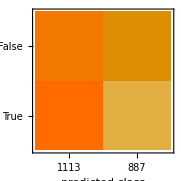
Classifier Measurements
Classifier method | NeuralNetwork
Number of test examples | 2000
Accuracy | (47.81.1) %
Accuracy baseline | (51.91.1) %
Geometric mean of probabilities | 0.488 ± 0.0022
Mean cross entropy | 0.718 ± 0.0045
Single evaluation time | 3.81 ms/example
Batch evaluation speed | 44.6 examples/ms
-Graphics- |

```mathematica
measurements=ClassifierMeasurements[classifier,testData]
```

```mathematica
(First@classifier)["Model"]["Network"]
```

NetChain[<>]

```mathematica
Information[classifier,"FunctionMemory"]
```

369. kB